```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics"],FontFamily->"Flama Light",FontSize->11]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
file40=FileNames["MSD-40suc-"<>"*.csv"];
file50=FileNames["MSD-50suc-"<>"*.csv"];
file70=FileNames["MSD-70suc-"<>"*.csv"];
```

```mathematica
data40=Table[Import[file40[[i]],"Data"][[2;;-1]],{i,Length[file40]}];
data50=Table[Import[file50[[i]],"Data"][[2;;-1]],{i,Length[file50]}];
data70=Table[Import[file70[[i]],"Data"][[2;;-1]],{i,Length[file70]}];
```

```mathematica
(*plot40=ListLinePlot[Table[data[[i,All,1;;2]],{i,Length[file40]}],
PlotStyle->Table[{Thickness[0.005],Opacity[1]},{i,Length[file40]}],
AspectRatio->1.5 GoldenRatio,
PlotRange->{{0,4},{0,2.5}},
FrameLabel->{{"MSD [µm^2]",None},{"Δt [sec]",None}},
FrameTicks->{{Range[0,3,0.5],None},{Range[0,4,1],None}},
Frame->True];*)
```

```mathematica
yaxis=Import[file40[[1]],"Data"][[1]]
```

{lag time [sec],MSD-longitudinal [um^2],MSD-transverse [um^2],MSAD-longitudinal [rad^2],MSAD-transverse [rad^2],MLAD [um x rad]}

```mathematica
verticalPlot=Function[{data,file,n},ListLinePlot[Table[data[[i,All,{1,n}]],{i,Length[file]}],
PlotStyle->Table[{Thickness[0.005],Opacity[1]},{i,Length[file]}],
AspectRatio->1.5 GoldenRatio,
PlotRange->{{0,4},{0,2}},
FrameLabel->{{yaxis[[n]],None},{"Δt [sec]",None}},
FrameTicks->{{Table[{i,ToString[NumberForm[i,{2,1}]]},{i,0,3,0.5}],None},{Range[0,4,1],None}},
Frame->True]];
```

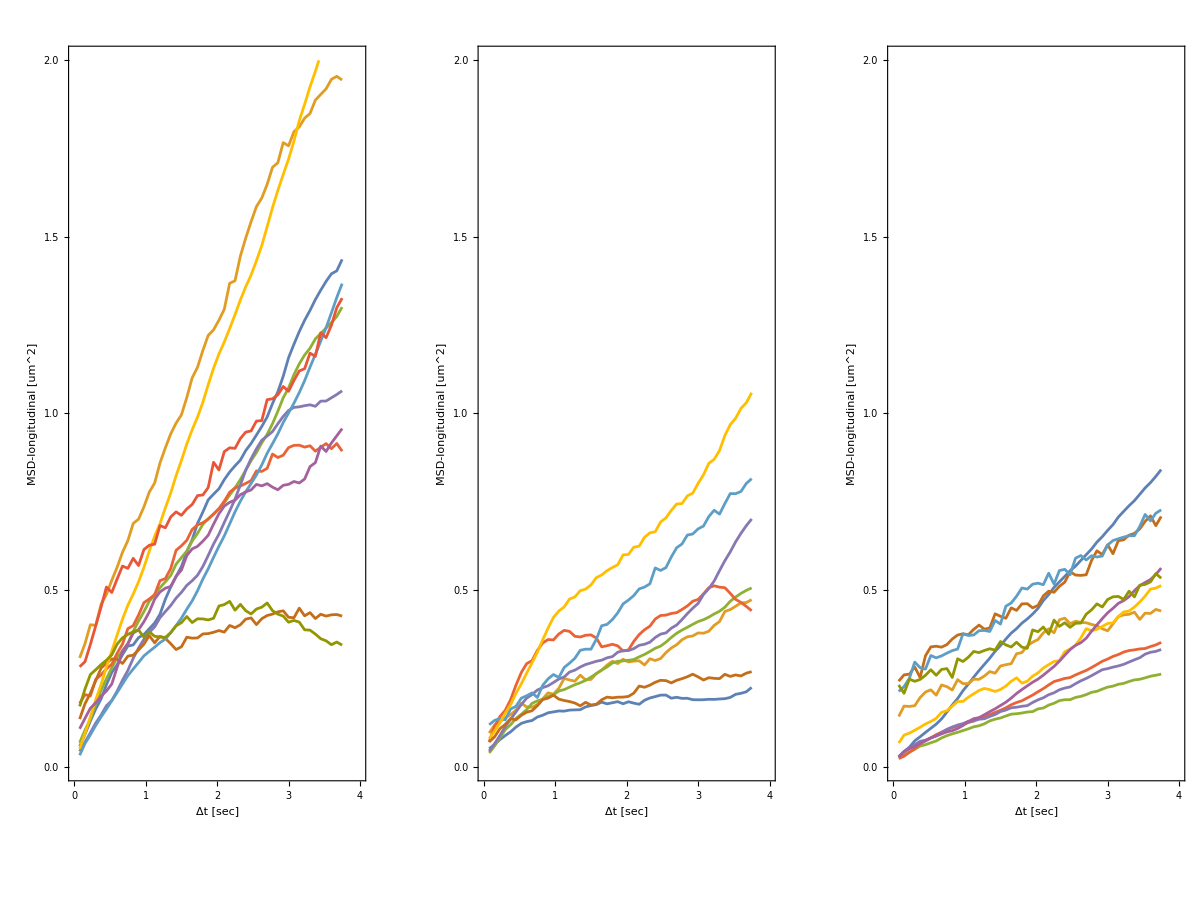

MSD-longitudinal [um^2].pdf

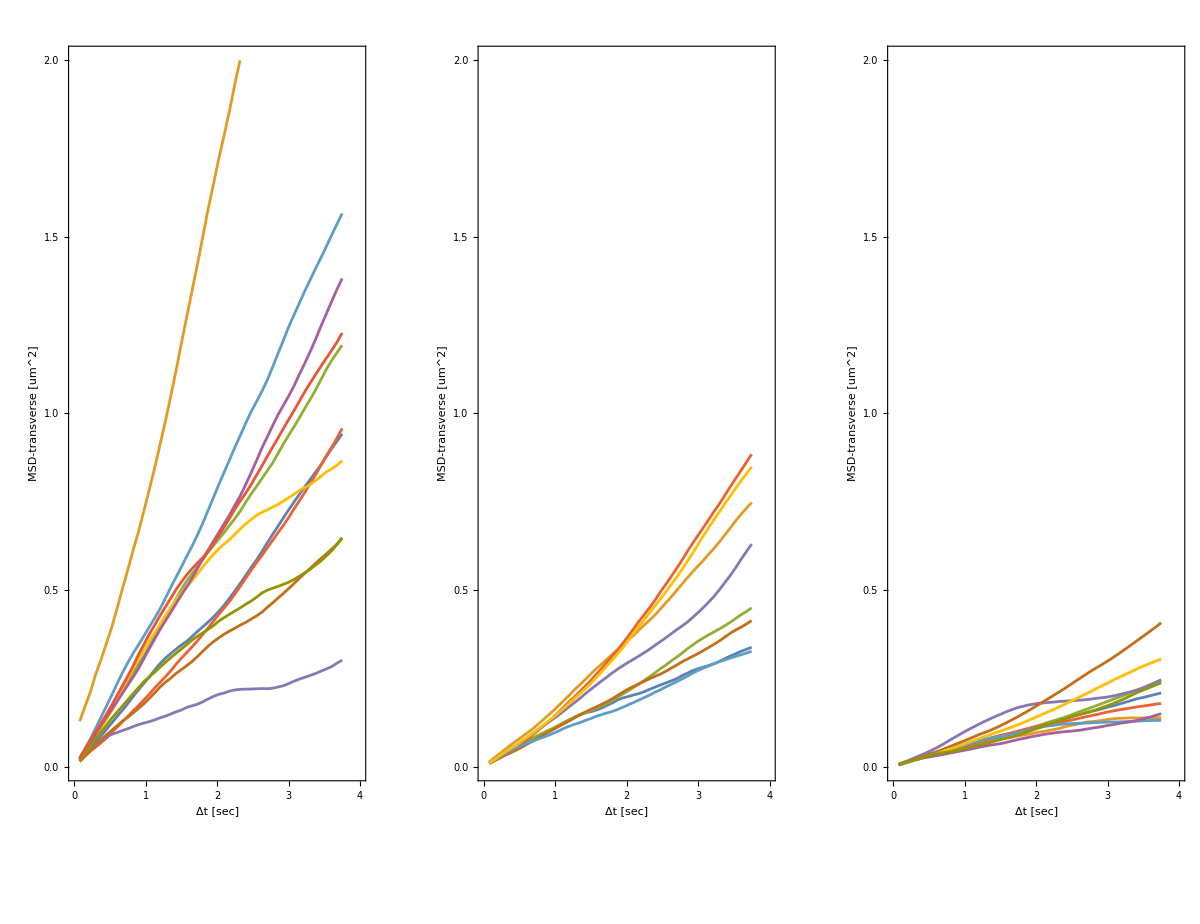

MSD-transverse [um^2].pdf

```mathematica
n=2;
GraphicsGrid[{{verticalPlot[data40,file40,n],verticalPlot[data50,file50,n],verticalPlot[data70,file70,n]}}]
Export[ToString[yaxis[[n]]]<>".pdf",%]

n=3;
GraphicsGrid[{{verticalPlot[data40,file40,n],verticalPlot[data50,file50,n],verticalPlot[data70,file70,n]}}]
Export[ToString[yaxis[[n]]]<>".pdf",%]
```

```mathematica
verticalPlot=Function[{data,file,n},ListLinePlot[Table[data[[i,All,{1,n}]],{i,Length[file]}],
PlotStyle->Table[{Thickness[0.005],Opacity[1]},{i,Length[file]}],
AspectRatio->1.5 GoldenRatio,
PlotRange->{{0,4},{0,16}},
FrameLabel->{{yaxis[[n]],None},{"Δt [sec]",None}},
FrameTicks->{{Table[{i,ToString[NumberForm[i,{2,1}]]},{i,0,16,4}],None},{Range[0,4,1],None}},
Frame->True]];
```

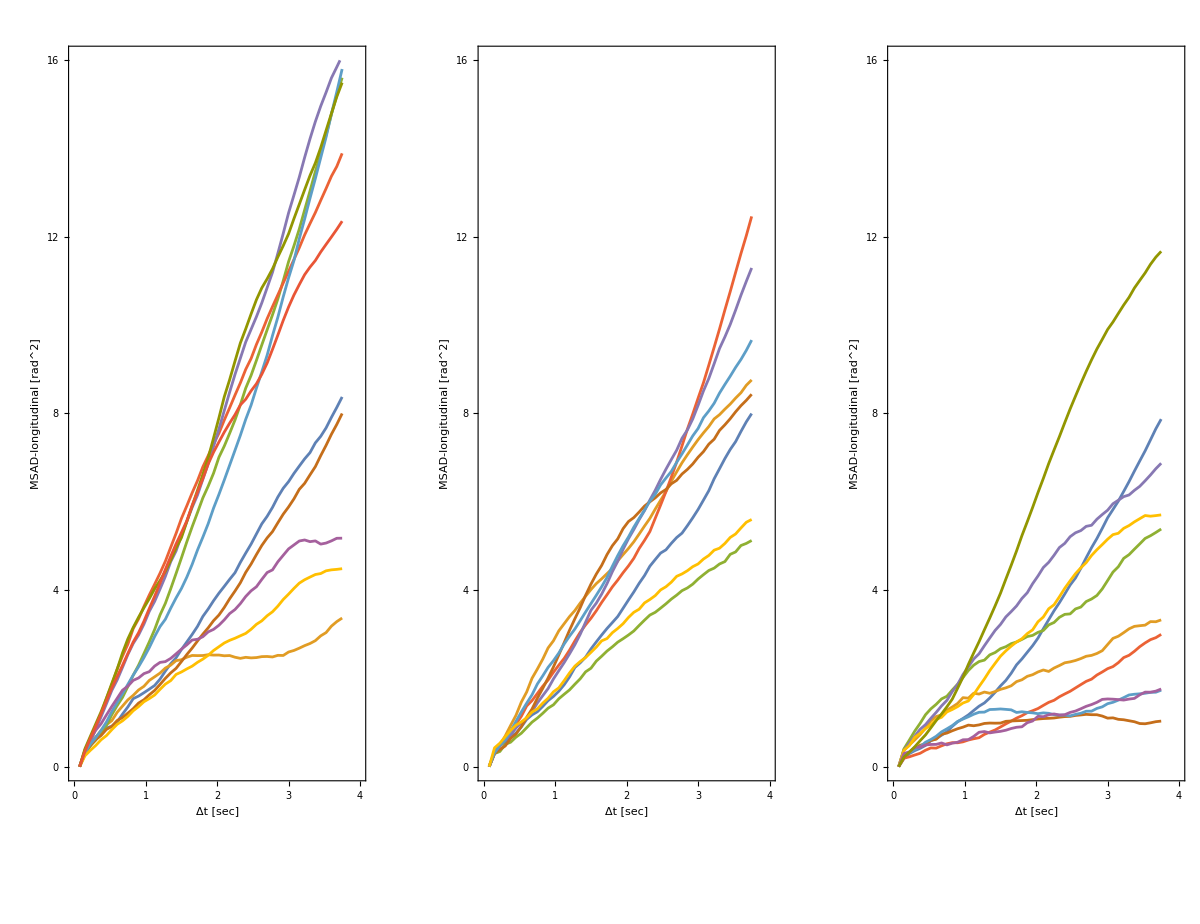

MSAD-longitudinal [rad^2].pdf

```mathematica
n=4;
GraphicsGrid[{{verticalPlot[data40,file40,n],verticalPlot[data50,file50,n],verticalPlot[data70,file70,n]}}]
Export[ToString[yaxis[[n]]]<>".pdf",%]
```

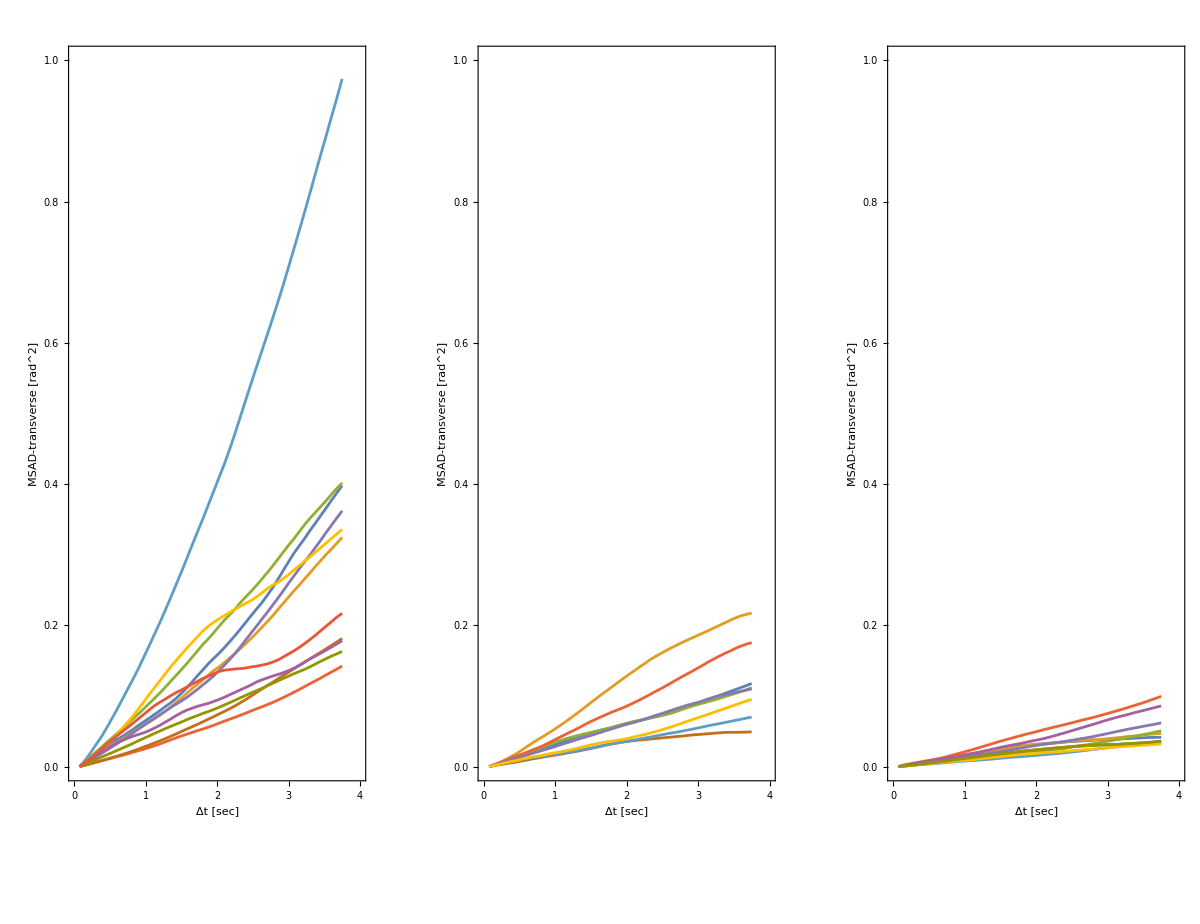

MSAD-transverse [rad^2].pdf

```mathematica
verticalPlot=Function[{data,file,n},ListLinePlot[Table[data[[i,All,{1,n}]],{i,Length[file]}],
PlotStyle->Table[{Thickness[0.005],Opacity[1]},{i,Length[file]}],
AspectRatio->1.5 GoldenRatio,
PlotRange->{{0,4},{0,1}},
FrameLabel->{{yaxis[[n]],None},{"Δt [sec]",None}},
FrameTicks->{{Table[{i,ToString[NumberForm[i,{2,1}]]},{i,0,1,0.2}],None},{Range[0,4,1],None}},
Frame->True]];
n=5;
GraphicsGrid[{{verticalPlot[data40,file40,n],verticalPlot[data50,file50,n],verticalPlot[data70,file70,n]}}]
Export[ToString[yaxis[[n]]]<>".pdf",%]
```

```mathematica
verticalPlot=Function[{data,file,n},ListLinePlot[Table[data[[i,All,{1,n}]],{i,Length[file]}],
PlotStyle->Table[{Thickness[0.005],Opacity[1]},{i,Length[file]}],
AspectRatio->1.5 GoldenRatio,
PlotRange->{{0,4},{-2,2}},
FrameLabel->{{yaxis[[n]],None},{"Δt [sec]",None}},
FrameTicks->{{Table[{i,ToString[NumberForm[i,{2,1}]]},{i,-2,2}],None},{Range[0,4,1],None}},
Frame->True]];
```

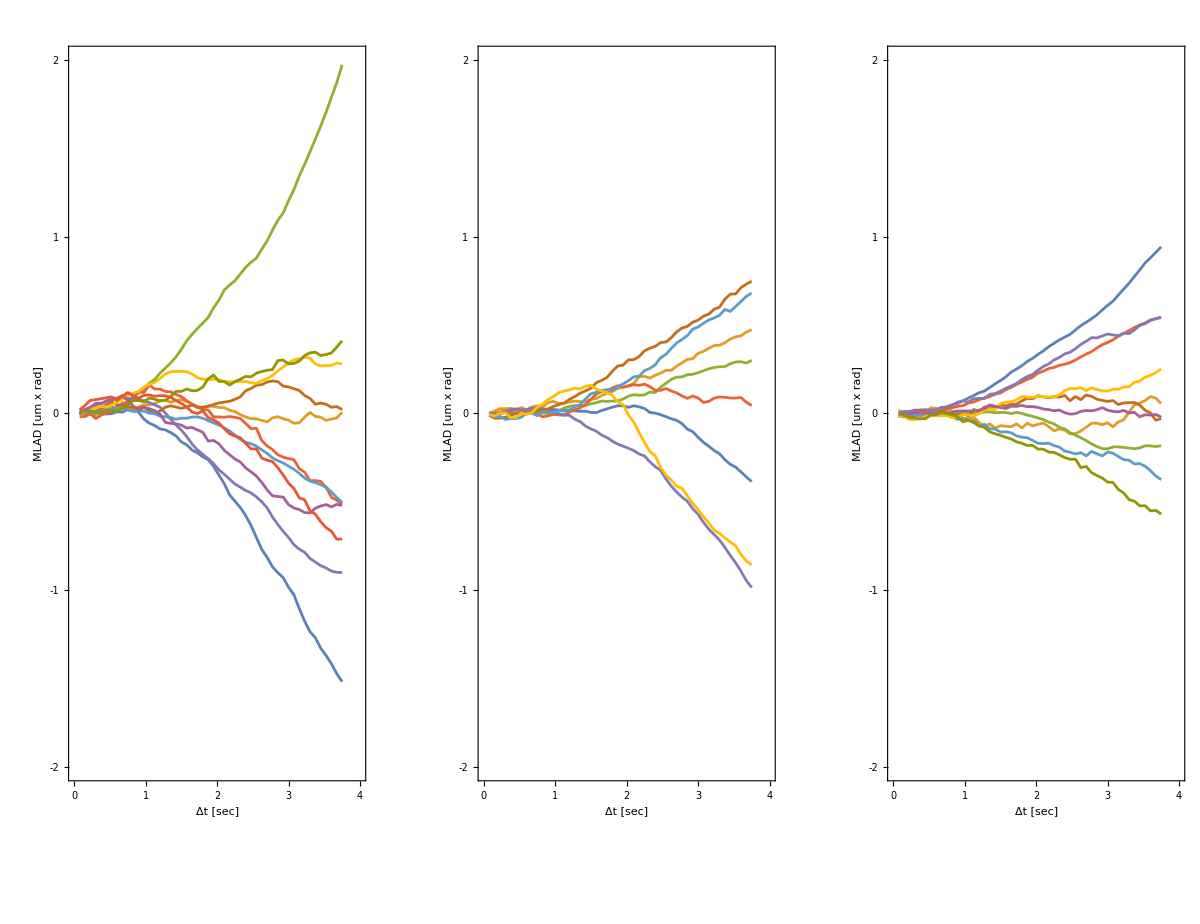

MLAD [um x rad].pdf

```mathematica
n=6;
GraphicsGrid[{{verticalPlot[data40,file40,n],verticalPlot[data50,file50,n],verticalPlot[data70,file70,n]}}]
Export[ToString[yaxis[[n]]]<>".pdf",%]
```